```mathematica
a=Sqrt[6]/4;
b=9-7*Sqrt[6]/2;
f[s_]=(a*s+b)^(-1);
```

We define a basis of so(5) and then take the tensor product with the standard basis to obtain a basis of the space of so(5)-valued 1-forms at a point.

```mathematica
A[j_,k_]:=Table[KroneckerDelta[j1,k]*KroneckerDelta[k1,j]-KroneckerDelta[j1,j]*KroneckerDelta[k1,k],{j1,1,5},{k1,1,5}];
matrixBasis = Flatten[Table[1/Sqrt[2]*A[j,k],{j,1,5},{k,1,j-1}],1];
basis = Flatten[Table[Table[TensorProduct[IdentityMatrix[5][[j]],matrixBasis[[k]]],{k,1,Length[matrixBasis]}],{j,1,5}],1];
innerProduct[Psi1_,Psi2_]:=Flatten[Psi1].Flatten[Psi2];
```

```mathematica
sigma=Table[A[1,j],{j,1,5}];
```

We estimate the three operators coming from curvature terms of the Weinkove solution: , and .
At , the matrices occurring in these expressions take the form  A[k,j],  r^2 A[1,k] if , else .

```mathematica
diffSigma[j_,k_]:=A[k,j]-A[j,k]
xSigma[j_,k_]:=KroneckerDelta[j,1]*sigma[[k]]-KroneckerDelta[k,1]*sigma[[j]]
comm[j_,k_]:=sigma[[j]].sigma[[k]]-sigma[[k]].sigma[[j]];
```

```mathematica
T1[Psi_]:=Table[Sum[diffSigma[j,k].Psi[[k]]-Psi[[k]].diffSigma[j,k],{k,1,5}],{j,1,5}]
T2[Psi_]:=Table[Sum[xSigma[j,k].Psi[[k]]-Psi[[k]].xSigma[j,k],{k,1,5}],{j,1,5}]
T3[Psi_]:=Table[Sum[comm[j,k].Psi[[k]]-Psi[[k]].comm[j,k],{k,1,5}],{j,1,5}]
```

```mathematica
t1=Table[innerProduct[T1[basis[[j]]],basis[[k]]],{j,1,Length[basis]},{k,1,Length[basis]}];
t2=Table[innerProduct[T2[basis[[j]]],basis[[k]]],{j,1,Length[basis]},{k,1,Length[basis]}];
t3=Table[innerProduct[T3[basis[[j]]],basis[[k]]],{j,1,Length[basis]},{k,1,Length[basis]}];
```

```mathematica
Eigenvalues[t1]
Eigenvalues[t2]
Eigenvalues[t3]
```

{6,6,6,6,6,4,4,4,4,4,4,4,4,4,4,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2}

{-√3,-√3,-√3,-√3,√3,√3,√3,√3,-√2,-√2,-√2,-√2,-√2,-√2,√2,√2,√2,√2,√2,√2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-3,-2,-2,-2,-2,-2,-2,-2,-2,-1,-1,-1,-1,-1,-1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0}

We can bound the operators  and  from above by their highest eigenvalue, respectively  and . In the two cells below, we introduce the matrix  which represents the action of , where $W$ is the Weinkove solution , on the space of so(5)-valued 1-forms at a point x with . Secondly, we cheaply estimate  by pointwise bounding each coefficient matrix by its highest eigenvalues. This is followed by a plot of the resulting bound , in red, and the highest eigenvalue of , which would be the best pointwise upper bound for this operator. One can see that the cheap estimate is quite sharp already.

```mathematica
M[r_]=f[r^2]^2*r^2*t3+f[r^2]*t1+2*r^2*f'[r^2]*t2;
MCheap[r_]=f[r^2]^2*r^2*1+f[r^2]*6-2*r^2*f'[r^2]*Sqrt[3];
max[r_]=Max[Eigenvalues[M[r]]];
```

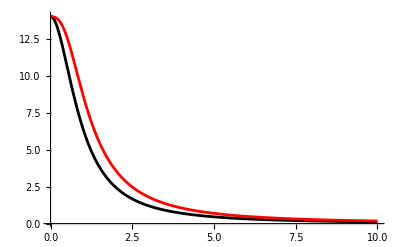

```mathematica
Plot[{max[r],MCheap[r]},{r,0,10},PlotRange->Full,PlotStyle->{Black,Red}]
```

In the following, we define a scalar potential bounding the potential of the operator  of interest, as in Section 5 of the accompanying paper. It depends on the degree l and an accompanying weight . The argument of the function below are the degree, the offset of  from  and .

```mathematica
V[deg_,off_,r_]=(2+deg*(deg+3))/r^2+1/16*(r^2-12)-2*Piecewise[{{deg+3,off=={-1,1}},{3,off=={0,1}},{2,off=={0,0}},{-deg,off=={1,1}}}]*f[r^2]+2*r^2*f[r^2]^2-2*MCheap[r];
```

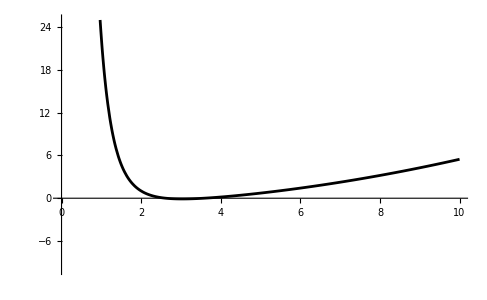

```mathematica
d0=6;
Plot[{V[d0,{-1,1},r]},{r,0,10},PlotRange->{-10,25},PlotStyle->Black]
```

Numerical determination of the lowest eigenvalue of the operator . This is not used in the paper’s arguments, but provides a quick justification for the list of low modes analyzed in greater detail in Section 4 of the accompanying paper.

Lowest approximate eigenvalue:0.578711

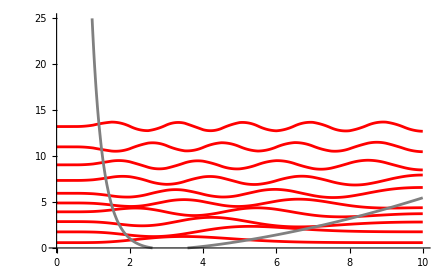

```mathematica
d0=6;off0={-1,1};
P=-u''[x]+V[d0,off0,x]*u[x];
{vals,funs}=NDEigensystem[P,u[x],{x,0,10},10];
Print["Lowest approximate eigenvalue:",vals[[1]]]
Plot[{vals+funs,V[d0,off0,x]},{x,0,10},PlotStyle->{Red,Gray},PlotRange->{0,25}]
```

Here we provide a numeric check of the estimates on the potential V_{6,(5,1)} in Lemma 5.1

```mathematica
Gam[x_,p_]= (4x+1)^((2p-1)/2)p^p Gamma[p]^2/((p-1)^(p-1)Gamma[2p]);

V65eff[r_]=V[6,{-1,1},r]- 56/r^2;
```

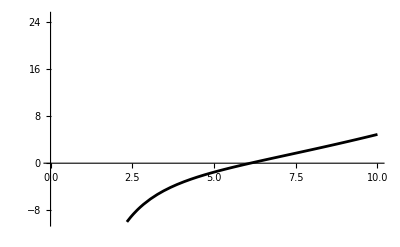

{r→6.10765}

```mathematica
Plot[{V65eff[r]},{r,0,10},PlotRange->{-10,25},PlotStyle->Black]
FindRoot[V65eff[r],{r,0.1}]
```

```mathematica
NIntegrate[r^7 V65eff[r]^4,{r,0,6.5}]
Floor[Gam[56,4]]
Floor[Gam[56,4]]-NIntegrate[r^7 V65eff[r]^4,{r,0,6.5}]
```

1.07929×10^7

11571428

778568.